```mathematica
Needs["ErrorBarPlots`"]
```

ErrorBar::shdw: Symbol ErrorBar appears in multiple contexts {ErrorBarPlots`,Global`}; definitions in context ErrorBarPlots` may shadow or be shadowed by other definitions.

ErrorListPlot::shdw: Symbol ErrorListPlot appears in multiple contexts {ErrorBarPlots`,Global`}; definitions in context ErrorBarPlots` may shadow or be shadowed by other definitions.

FittedModel[22.1113 x+4.11445]

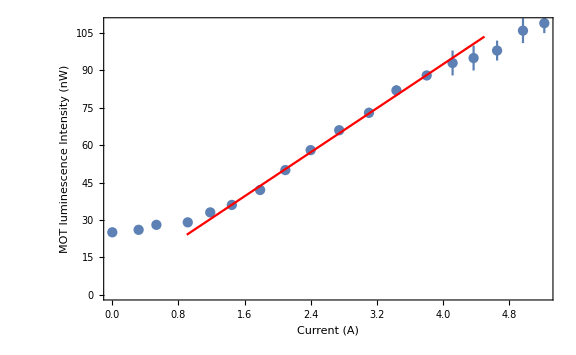

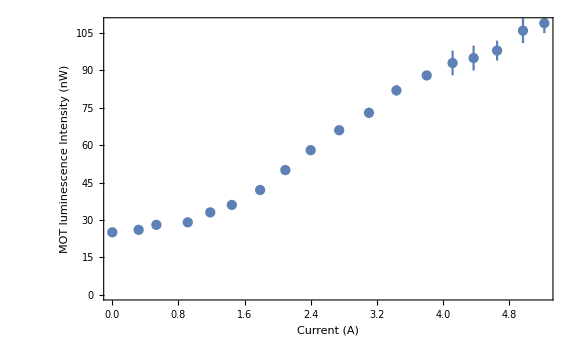

| Estimate | Standard Error | t-Statistic | P-Value
1 | 4.11445 | 1.53539 | 2.67974 | 0.0315511
x | 22.1113 | 0.529295 | 41.775 | 1.17476×10^-9

```mathematica
magnet =  {{5.223,0.581, 0.004},{4.965, 0.584, 0.005},{4.652, 0.592, 0.004},{4.368,0.595,0.005},{4.114,0.597,0.005},{3.801,0.602,0.001},{3.435,0.608,0.002},{3.103,0.617,0.002},{2.743,0.624,0.001},{2.398,0.632,0.001},{2.092,0.640,0.001},{1.787,0.648,0.002},{1.445,0.654,0.001},{1.184,0.657,0.001},{0.912,0.661,0.001},{0.533,0.662,0.001},{0.318,0.664,0.001},{0.000,0.665,0.001}};
magnetError ={{#[[1]],(0.69- #[[2]])*1000},ErrorBar[#[[3]]*1000]} &/@magnet;
lf = LinearModelFit[Map[{#[[1,1]], #[[1,2]]}&, magnetError[[5;;13]]],{1,x}, x] 
Show[ErrorListPlot[magnetError],  Plot[lf[x], {x, 0.9, 4.5},PlotStyle->Red],Frame->{{True,False},{True,False}},FrameLabel->{Style["Current (A)",Medium],Style["MOT luminescence Intensity (nW)",Medium]}, ImageSize->Large]
Show[ErrorListPlot[magnetError],Frame->{{True,False},{True,False}},FrameLabel->{Style["Current (A)",Medium],Style["MOT luminescence Intensity (nW)",Medium]}, ImageSize->Large]
lf["ParameterTable"]
```

FittedModel[0.748259 erfc(4.68092 x-0.336472)+0.0066357]

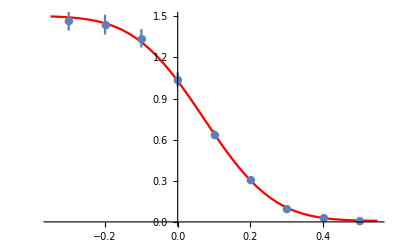

| Estimate | Standard Error | t-Statistic | P-Value
A | 0.748259 | 0.0163924 | 45.6468 | 9.52844×10^-8
B | 4.68092 | 0.0949346 | 49.3067 | 6.48426×10^-8
CC | 0.336472 | 0.0330774 | 10.1723 | 0.000157495
DD | 0.0066357 | 0.000502064 | 13.2168 | 0.0000442987

```mathematica
beampower = {{39.7, 1.47},{39.8, 1.44},{39.9,1.34},{40,1.04},{40.1,0.64},{40.2,0.31},{40.3,0.1},{40.4, 0.03},{40.5, 0.01}};
beampowerError = Map[{{#[[1]], #[[2]]},ErrorBar[#[[2]]*0.05]} &,beampower];
errors =Map[Max[#[[2]],0.01]*0.05&, beampower];
nlm = NonlinearModelFit[Map[{#[[1]]-40,#[[2]]} &, beampower],A*Erfc[B*x-CC]+DD, {{A,0.735},{B,4.942},{CC,0},{DD,0.012}},x, Weights->100/errors^2]
Show[Plot[nlm[x],{x,-0.35,0.55},PlotStyle->Red],ErrorListPlot[Map[{{#[[1, 1]] - 40, #[[1, 2]]},#[[2]]} &, beampowerError],PlotMarkers->{Automatic,Tiny}]]
nlm["ParameterTable"]
```

FittedModel[0.748259 erfc(4.68092 x-187.573)+0.0066357]

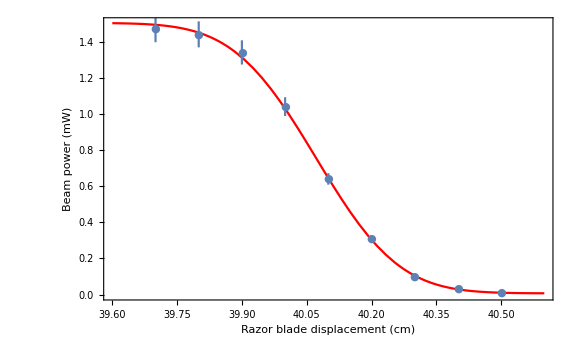

| Estimate | Standard Error | t-Statistic | P-Value
A | 0.748259 | 0.0163924 | 45.6468 | 9.52844×10^-8
B | 4.68092 | 0.0949346 | 49.3067 | 6.48426×10^-8
CC | 187.573 | 3.82852 | 48.9936 | 6.69377×10^-8
DD | 0.0066357 | 0.000502064 | 13.2168 | 0.0000442987

0.302123

0.00612742

```mathematica
nlm2 = NonlinearModelFit[Map[{#[[1]],#[[2]]} &, beampower],A*Erfc[B*x-CC]+DD, {{A,0.7},{B,4.94},{CC,193.6},{DD,0.01}},x, Weights -> 1/errors^2]
Show[Plot[nlm2[x],{x,39.6,40.6},PlotStyle->Red],ErrorListPlot[Map[{{#[[1, 1]] , #[[1, 2]]},#[[2]]} &, beampowerError],PlotMarkers->{Automatic,Tiny}],Frame->{{True,False},{True,False}},FrameLabel->{Style["Razor blade displacement (cm)",Medium],Style["Beam power (mW)",Medium]}, ImageSize->Large]
nlm2["ParameterTable"]
Bfit=B/.nlm2["BestFitParameters"];
W= Sqrt[2]/Bfit
errW = Sqrt[2]/(Bfit)^2 *nlm2["ParameterErrors"][[2]]
```

FittedModel[74.8649 cos^2(7.06221-(π x)/180)+9.762]

| Estimate | Standard Error | t-Statistic | P-Value
A | 74.8649 | 5.35743 | 13.974 | 2.05204×10^-15
B | 404.635 | 2.05008 | 197.375 | 2.78183×10^-52
CC | 9.762 | 3.28074 | 2.97555 | 0.00543782

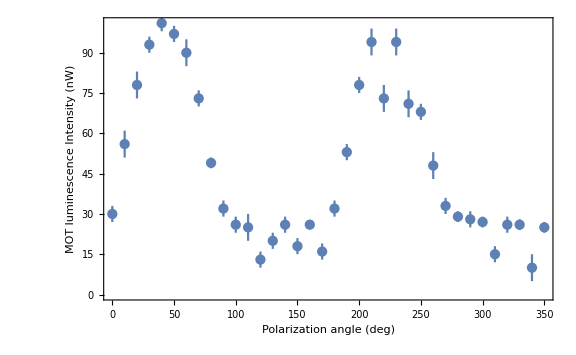

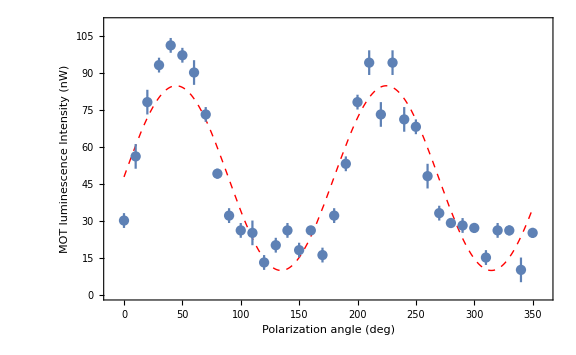

```mathematica
polarizationRaw = Map[{#[[1]],#[[2]],#[[3]]}&,{{0, 660,3},{10,634,5},{20,612,5},{30,597,3},{40,589,3},{50,593,3},{60,600,5},{70,617,3},{80,641,2},{90,658,3},{100,664,3},{110,665,5},{120,677,3},{130,670,3},{140,664,3},{150,672,3},{160,664,1},{170,674,3},{180,658,3},{190,637,3},{200,612,3},{210,596,5},{220,617,5},{230,596,5},{240,619,5},{250,622,3},{260,642,5},{270,657,3},{280,661,2},{290,662,3},{300,663,2},{310,675,3},{320,664,3},{330,664,2},{340,680,5},{350,665,2}}];
polarization = Map[{#[[1]], 690-#[[2]], #[[3]]}&, polarizationRaw];
error = Map[#[[3]]&,polarization];
fit = NonlinearModelFit[Map[{#[[1]],#[[2]]}&,polarization],A*Cos[Pi*x/180-Pi*B/180]^2+CC,{{A,86.9},B, {CC,591.55}},x]
fit["ParameterTable"]
Show[ErrorListPlot[Map[{{#[[1]],#[[2]]},ErrorBar[#[[3]]]}&,polarization]],Frame->{{True,False},{True,False}},FrameLabel->{Style["Polarization angle (deg)",Medium],Style["MOT luminescence Intensity (nW)",Medium]},ImageSize->Large]
Show[Plot[fit[x],{x,0,350},PlotStyle->{Red,Thin,Dashed},PlotRange->{{-10,360},{0,110}}],ErrorListPlot[Map[{{#[[1]],#[[2]]},ErrorBar[#[[3]]]}&,polarization]],Frame->{{True,False},{True,False}},FrameLabel->{Style["Polarization angle (deg)",Medium],Style["MOT luminescence Intensity (nW)",Medium]},ImageSize->Large]
```

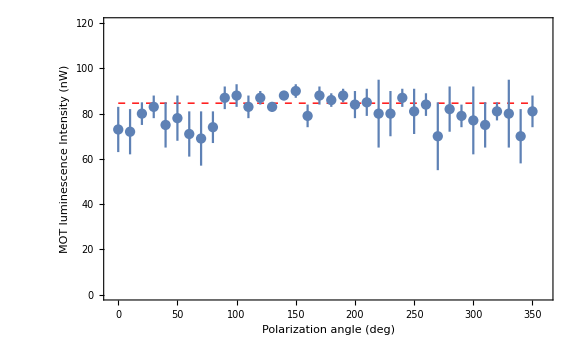

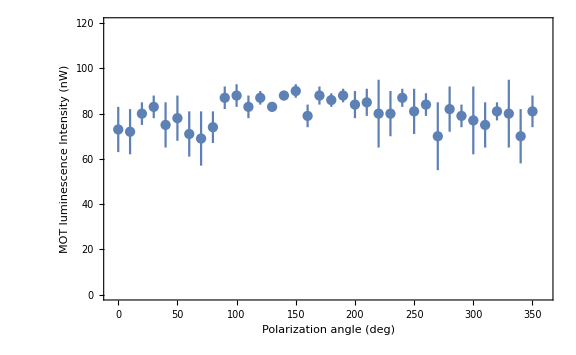

```mathematica
secondWaveplateRaw = {{0, 617, 10},{10,618,10},{20,610,5},{30,607,5},{40,615,10},{50,612,10},{60,619,10},{70,621,12},{80,616,7},{90,603,5},{100,602,5},{110,607,5},{120,603,3},{130,607,2},{140,602,2},{150,600,3},{160,611,5},{170,602,4},{180,604,3},{190,602,3},{200,606,6},{210,605,6},{220,610,15},{230,610,10},{240,603,4},{250,609,10},{260,606,5},{270,620,15},{280,608,10},{290,611,5},{300,613,15},{310,615,10},{320,609,4},{330,610,15},{340,620,12},{350,609,7}};
secondWaveplate = Map[{#[[1]], 690 - #[[2]], #[[3]]}&, secondWaveplateRaw];
errs = Map[#[[3]]&,secondWaveplate];
line=NonlinearModelFit[Map[{#[[1]],#[[2]]}&,secondWaveplate],A,A,x,Weights->1/errs^2];
Show[Plot[line[x],{x,0,350},PlotRange->{{-5,360},{0,120}},PlotStyle->{Red,Dashed,Thin}],ErrorListPlot[Map[{{#[[1]],#[[2]]},ErrorBar[#[[3]]]}&,secondWaveplate],PlotRange->{{-5,360},{0,120}}],Frame->{{True,False},{True,False}},FrameLabel->{Style["Polarization angle (deg)",Medium],Style["MOT luminescence Intensity (nW)",Medium]},ImageSize->Large]
Show[ErrorListPlot[Map[{{#[[1]],#[[2]]},ErrorBar[#[[3]]]}&,secondWaveplate],PlotRange->{{-5,360},{0,120}}],Frame->{{True,False},{True,False}},FrameLabel->{Style["Polarization angle (deg)",Medium],Style["MOT luminescence Intensity (nW)",Medium]},ImageSize->Large]
```